# Midterm 3

Note: If you get to a part where you know exactly what you need to do but don’t know how to make Mathematica do it, please write clearly and explicitly what you would do. We will give you at least partial credit for correct reasoning even if the code doesn’t quite work. (But do your best to get the code to work! All Mathematica techniques you will need for this exam you have already seen in some form in the homework.)

## Problem 4 (25 points)

You are standing on a large, flat turntable that makes one revolution each minute in a counterclockwise direction when viewed from above (see figure below). A ball launcher is mounted 15 m from the center of the turntable. Your goal is to launch a ball across the turntable so that it lands on a target located 15 beyond the center of the turntable from your position, marked by the X in the figure. A straight line drawn from the ball launcher to the target passes through the center of the turntable. In this problem, you will determine a set of launch velocity components that will ensure the ball hits the target.

-Graphics-

I’m not feeling like an evil physicist for this problem, so you may ignore air resistance and the rotational effects of the earth. Because we are ignoring the earth’s rotation, the equations given in Equation 9.53 of the textbook are NOT the right ones to use. Instead, you will need to determine the appropriate equations of motion (i.e. differential equations for x, y, and z) for this situation. Let x and y be rotating in the plane of the turntable as shown in the figure, and z coming directly out of the page (i.e. pointing vertically up, against the force of gravity).

```mathematica
Quit[]
Clear["*"]
```

## Part A: Qualitative Analysis

If you use launch settings that result in the ball hitting the target when the turntable is NOT moving, will you hit the target when the turntable IS moving? If not, describe qualitatively where the ball would land relative to the target.

Your answer here: 
No the ball would not hit the target. Consider for example how snipers have to take the Coriolis force into account when taking long range shots. A similar thing would happen here and the ball would land to the right of the target. (right in this situation means the y value of the final position vector would be negative instead of zero like we want.)

## Part B: Set up the equations of motion

Determine the equations of motion whose solutions give the ball’s trajectory as measured by someone standing on the turntable. If it’s easier for you to work it out by hand, please include your clearly labeled work with your written submission, and then write down your Mathematica equations here. Define the z direction to be positive in the vertically upward direction. Use the symbol g for the acceleration due to gravity and Omega for the turntable’s rotational speed. You will input the numerical values of g and Omega in subsequent cells.

```mathematica
(*Turntable rotational speed*)
OmegaVec = Omega*{0, 0, 1}
(*position vector and its derivative as a funciton of time*)
r[t] = {x[t], y[t], z[t]}
r'[t] = {x'[t], y'[t], z'[t]}
(*centrifucal force we exclude mass since it divides out anyway*)
Fcf = Cross[Cross[OmegaVec, r[t]], OmegaVec]
(* coriollis force, again we exclude the mass as it divides out*)
Fcor = 2*Cross[r'[t], OmegaVec]
(* force of gravity again we exclude the mass*)
Fgrav = g*{0, 0, -1}
(* no we define our equations of motion*)
Xeq=x''[t]==Fgrav[[1]]+ Fcf[[1]] + Fcor[[1]]
Yeq=y''[t]==Fgrav[[2]]+ Fcf[[2]] + Fcor[[2]]
Zeq=z''[t]==Fgrav[[3]]+ Fcf[[3]] + Fcor[[3]]
```

{0,0,Omega}

{x[t],y[t],z[t]}

{x'[t],y'[t],z'[t]}

{Omega^2 x[t],Omega^2 y[t],0}

{2 Omega y'[t],-2 Omega x'[t],0}

{0,0,-g}

x''[t]==Omega^2 x[t]+2 Omega y'[t]

y''[t]==Omega^2 y[t]-2 Omega x'[t]

z''[t]==-g

Solve for the numerical value of Omega

```mathematica
(* 1 revolution per minute gives us  in other words 2Pi rads/min -> 2pi rads /min* 1 min / 60 seconds -> Pi/30 rads/sec*)
OmegaValue = Pi/ 30
```

π/30

Write down the initial position of the ball as a vector r0.

```mathematica
r0={-15,0,0}
```

{-15,0,0}

## Part C: Find a launch velocity that allows the ball to hit the target

To make things a little simpler, let’s say that the vertical component of the initial velocity is 10 m/s. Play around with the other components of the initial velocity v0 until you find an initial velocity that allows the ball to hit the target to within 0.1 m in the x and y directions.

Z

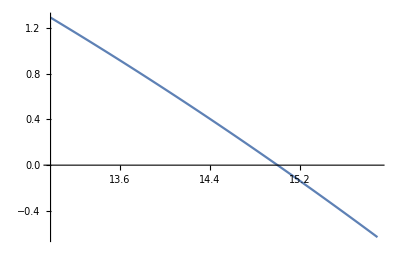

Y

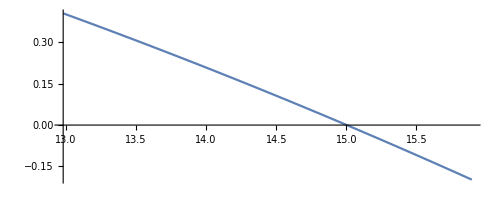

```mathematica
v0={14.55,3.13,10};

sol=NDSolve[{Xeq,Yeq,Zeq,x[0]==r0[[1]],y[0]==r0[[2]],z[0]==r0[[3]],x'[0]==v0[[1]],y'[0]==v0[[2]],z'[0]==v0[[3]]}/.{g->9.81,Omega->OmegaValue},{x,y,z},{t,0,5}];

(* I'm giving you one ParametricPlot to help you visualize the solution. You will likely want to generate at least one more ParametricPlot to ensure you are hitting the target. *)
tStart = 1.9;
tEnd = 2.1;
(* at x = 15, z = 0 and at x = 15, y = 0*)
Print["Z"]
ParametricPlot[{x[t],z[t]}/.sol,{t,tStart,tEnd}]
Print["Y"]
ParametricPlot[{x[t],y[t]}/.sol,{t,tStart,tEnd}]
```

Initial Velocity: 
v0=[14.55, 3.13, 10]

## Bonus (2 points)

Find an initial velocity that will cause the ball to land directly back on the ball launcher after the turntable has completed precisely one half of a revolution during the ball’s time in the air.

## Additional work for any of the written problems (label each one clearly)

```mathematica
Quit[]
```

Calculations for question 2:
Part C:

```mathematica
MassMat = m*IdentityMatrix[4];
KMat = k* { {2, -1, 0, 0}, {-1, 2, -1, 0}, {0, -1, 2, -1}, {0, 0, -1, 2}   };
MinvK = Inverse[MassMat].KMat;MinvK//MatrixForm
Print["Square of Normal Modes (i.e. ω^2)"]
Eigensystem[MinvK][[1]]//MatrixForm
Print["Corresponding normal mode oscillation patterns"]
Vecs = Eigensystem[MinvK][[2]];
Vecs[[1]]//MatrixForm
Vecs[[2]]//MatrixForm
Vecs[[3]]//MatrixForm
Vecs[[4]]//MatrixForm
```

((2 k)/m | -k/m | 0 | 0
-k/m | (2 k)/m | -k/m | 0
0 | -k/m | (2 k)/m | -k/m
0 | 0 | -k/m | (2 k)/m)

Square of Normal Modes (i.e. ω^2)

(((5+√5) k)/(2 m)
((3+√5) k)/(2 m)
((5-√5) k)/(2 m)
((3-√5) k)/(2 m))

Corresponding normal mode oscillation patterns

(-1
1/2 (1+√5)
1/2 (-1-√5)
1)

(1
1/2 (1-√5)
1/2 (1-√5)
1)

(-1
1/2 (1-√5)
1/2 (-1+√5)
1)

(1
1/2 (1+√5)
1/2 (1+√5)
1)

Part D:

```mathematica
MassMat = IdentityMatrix[4];
MassMat[[2]][[2]] =2;
MassMat[[3]][[3]] = 2;
MassMat = m * MassMat
MassMat//MatrixForm
KMat = k* { {2, -1, 0, 0}, {-1, 2, -1, 0}, {0, -1, 2, -1}, {0, 0, -1, 2}   };
MinvK = Inverse[MassMat].KMat;MinvK//MatrixForm
Print["Square of Normal Modes (i.e. ω^2)"]
Eigensystem[MinvK][[1]]//MatrixForm
Print["Corresponding normal mode oscillation patterns"]
Vecs = Eigensystem[MinvK][[2]];
Vecs[[1]]//MatrixForm
Vecs[[2]]//MatrixForm
Vecs[[3]]//MatrixForm
Vecs[[4]]//MatrixForm
```

{{m,0,0,0},{0,2 m,0,0},{0,0,2 m,0},{0,0,0,m}}

(m | 0 | 0 | 0
0 | 2 m | 0 | 0
0 | 0 | 2 m | 0
0 | 0 | 0 | m)

((2 k)/m | -k/m | 0 | 0
-k/(2 m) | k/m | -k/(2 m) | 0
0 | -k/(2 m) | k/m | -k/(2 m)
0 | 0 | -k/m | (2 k)/m)

Square of Normal Modes (i.e. ω^2)

((5 k)/(2 m)
((5+√17) k)/(4 m)
k/m
((5-√17) k)/(4 m))

Corresponding normal mode oscillation patterns

(-2
1
-1
2)

(1
1/4 (3-√17)
1/4 (3-√17)
1)

(-1
-1
1
1)

(1
1/4 (3+√17)
1/4 (3+√17)
1)

Calculations for question 3
Part A:

```mathematica
sigma = sigma0(1 + x/a);
M = Integrate[Integrate[sigma, {y, 0, -b*x/a + b}], {x, 0, a}];
Print["Mass:"]
Print[M]
```

Mass:

(2 a b sigma0)/3

Part C:

```mathematica
Jxx = Integrate[Integrate[sigma*x^2, {y, 0, -b*x/a + b}], {x, 0, a}]
Jyy = Integrate[Integrate[sigma*y^2, {y, 0, -b*x/a + b}], {x, 0, a}]
Jxy = Integrate[Integrate[sigma*x*y, {y, 0, -b*x/a + b}], {x, 0, a}]
Jxz = 0;
Jyz = 0;
Jzz = 0;

InTen = FullSimplify[{{Jyy,  -Jxy, 0}, {-Jxy,  Jxx, 0}, {0, 0,  Jxx + Jyy}}];
InTen//MatrixForm
Eigensystem[InTen/.{a->1, b->1, sigma0->1}]
```

2/15 a^3 b sigma0

1/10 a b^3 sigma0

7/120 a^2 b^2 sigma0

(1/10 a b^3 sigma0 | -7/120 a^2 b^2 sigma0 | 0
-7/120 a^2 b^2 sigma0 | 2/15 a^3 b sigma0 | 0
0 | 0 | 1/30 b (4 a^3+3 a b^2) sigma0)

{{7/30,1/120 (14+√53),1/120 (14-√53)},{{0,0,1},{1/7 (2-√53),1,0},{1/7 (2+√53),1,0}}}

Part D:

```mathematica
InTen1 = FullSimplify[m*{{3*b^2/20, -7*a*b/80, 0}, {-7*a*b/80, a^2/5, 0}, {0, 0, (4*a^2 + 3b^2)/ 20   }}];
InTen1//MatrixForm
vals = {a->1/4, b->1/4, m->1};
InTen1 = InTen1/.vals;
InTen1//MatrixForm
ES = Eigensystem[InTen1]
ES[[1]][[1]]
ES[[1]][[2]]
ES[[1]][[3]]
ES[[2]][[1]]
ES[[2]][[2]]
ES[[2]][[3]]
```

((3 b^2 m)/20 | -7/80 a b m | 0
-7/80 a b m | (a^2 m)/5 | 0
0 | 0 | 1/20 (4 a^2+3 b^2) m)

(3/320 | -7/1280 | 0
-7/1280 | 1/80 | 0
0 | 0 | 7/320)

{{7/320,(14+√53)/1280,(14-√53)/1280},{{0,0,1},{1/7 (2-√53),1,0},{1/7 (2+√53),1,0}}}

7/320

(14+√53)/1280

(14-√53)/1280

{0,0,1}

{1/7 (2-√53),1,0}

{1/7 (2+√53),1,0}

Part G:
Calculating rotational energy

```mathematica
omega = 33.8958*{1/Sqrt[2], 1/Sqrt[2], 0};
Trot = 1/2 * Dot[omega, Dot[InTen1, omega]]
```

3.14159

Additional Calculations for question 2
Part 1, equal masses:

```mathematica
Quit[]
Clear["*"]
```

```mathematica
T = (m1*x1dot^2 + m2*x2dot^2 + m3*x3dot^2 + m4*x4dot^2)/2;
U =k*(x1^2 + (x1 - x2)^2 + (x2 - x3)^2 + (x3 - x4)^2 + x4^2)/2;
L = T - U;
rule = {x1->x1[t], x2->x2[t], x3->x3[t], x4->x4[t], x1dot->x1'[t], x2dot-> x2'[t], x3dot->x3'[t], x4dot->x4'[t]};
p1 = D[L, x1dot]/.rule;
p2 = D[L, x2dot]/.rule;
p3 = D[L, x3dot]/.rule;
p4 = D[L, x4dot]/.rule;
dLdx1 = D[L, x1]/.rule;
dLdx2 = D[L, x2]/.rule;
dLdx3 = D[L, x3]/.rule;
dLdx4 = D[L, x4]/.rule;

eq1 = dLdx1 == D[p1, t]
eq2 = dLdx2 == D[p2, t]
eq3 = dLdx3 == D[p3, t]
eq4 = dLdx4 == D[p4, t]
```

-1/2 k (2 x1[t]+2 (x1[t]-x2[t]))==m1 x1''[t]

-1/2 k (-2 (x1[t]-x2[t])+2 (x2[t]-x3[t]))==m2 x2''[t]

-1/2 k (-2 (x2[t]-x3[t])+2 (x3[t]-x4[t]))==m3 x3''[t]

-1/2 k (-2 (x3[t]-x4[t])+2 x4[t])==m4 x4''[t]

1

1

1

«2 more identical outputs»

{x1[0]==-1,x2[0]==1/2 (1+√5),x3[0]==1/2 (-1-√5),x4[0]==1,x1'[0]==0,x2'[0]==0,x3'[0]==0,x4'[0]==0}

{{x1[t]→InterpolatingFunction[…][t],x2[t]→InterpolatingFunction[…][t],x3[t]→InterpolatingFunction[…][t],x4[t]→InterpolatingFunction[…][t]}}

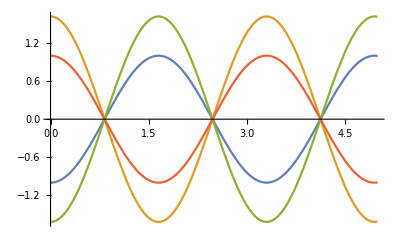

```mathematica
m1=1
m2=1
m3=1
m4=1
k=1
IC = { x1[0]==-1, x2[0]==1/2 (1+√5), x3[0]==-1/2 (1+√5), x4[0]==1, x1'[0]==0, x2'[0]==0, x3'[0]==0, x4'[0]==0 }
sol1 = NDSolve[{eq1, eq2, eq3, eq4, IC}, {x1[t], x2[t], x3[t], x4[t]}, {t, 0, 5}]
Plot[{x1[t]/.sol1, x2[t]/.sol1, x3[t]/.sol1, x4[t]/.sol1}, {t, 0, 5}]
```

Part 2:
outer masses with mass m and inner masses 2m

```mathematica
Quit[]
Clear["*"]
```

```mathematica
T = (m1*x1dot^2 + m2*x2dot^2 + m3*x3dot^2 + m4*x4dot^2)/2;
U =k*(x1^2 + (x1 - x2)^2 + (x2 - x3)^2 + (x3 - x4)^2 + x4^2)/2;
L = T - U;
rule = {x1->x1[t], x2->x2[t], x3->x3[t], x4->x4[t], x1dot->x1'[t], x2dot-> x2'[t], x3dot->x3'[t], x4dot->x4'[t]};
p1 = D[L, x1dot]/.rule;
p2 = D[L, x2dot]/.rule;
p3 = D[L, x3dot]/.rule;
p4 = D[L, x4dot]/.rule;
dLdx1 = D[L, x1]/.rule;
dLdx2 = D[L, x2]/.rule;
dLdx3 = D[L, x3]/.rule;
dLdx4 = D[L, x4]/.rule;

eq1 = dLdx1 == D[p1, t]
eq2 = dLdx2 == D[p2, t]
eq3 = dLdx3 == D[p3, t]
eq4 = dLdx4 == D[p4, t]
```

-1/2 k (2 x1[t]+2 (x1[t]-x2[t]))==m1 x1''[t]

-1/2 k (-2 (x1[t]-x2[t])+2 (x2[t]-x3[t]))==m2 x2''[t]

-1/2 k (-2 (x2[t]-x3[t])+2 (x3[t]-x4[t]))==m3 x3''[t]

-1/2 k (-2 (x3[t]-x4[t])+2 x4[t])==m4 x4''[t]

1

2

2

1

1

{x1[0]==-2,x2[0]==1,x3[0]==-1,x4[0]==2,x1'[0]==0,x2'[0]==0,x3'[0]==0,x4'[0]==0}

{{x1[t]→InterpolatingFunction[…][t],x2[t]→InterpolatingFunction[…][t],x3[t]→InterpolatingFunction[…][t],x4[t]→InterpolatingFunction[…][t]}}

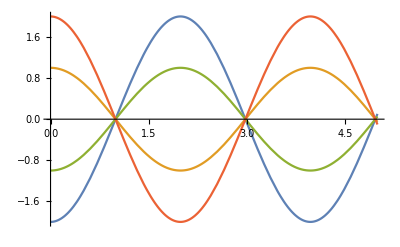

```mathematica
m1=1
m2=2
m3=2
m4=1
k=1
IC = { x1[0]==-2, x2[0]==1, x3[0]==-1, x4[0]==2, x1'[0]==0, x2'[0]==0, x3'[0]==0, x4'[0]==0 }
sol1 = NDSolve[{eq1, eq2, eq3, eq4, IC}, {x1[t], x2[t], x3[t], x4[t]}, {t, 0, 5}]
Plot[{x1[t]/.sol1, x2[t]/.sol1, x3[t]/.sol1, x4[t]/.sol1}, {t, 0, 5}]
```